# Visualizing Multivariable Functions in Chemistry Using Mathematica

Mathematica can aid visualization of 3D and 4D objects that are difficult for human brains, and therefore early chemistry students.

Madeleine Sutherland, Jun. 24,  2018

Several types of functions can be particularly challenging for beginning chemistry students to visualize.   In Thermochemistry, students need to visualize contour plots made from series of isotherms.  In elementary quantum chemistry, hydrogen wavefunctions and probability functions are four-dimensional and students need to visualize the locations of the zero’s (nodes).

## I. Critical points of a gas, from thermochemistry

Start by explaining the basics ...

Adapted from a Physical Chemistry homework problem by Professor Andrew Berke at Smith College.

Background: Ideal gases follow the relationship PV=nRT (or PVbar=RT), but as pressure increases, molecules of gas interact more and behave non-ideally. So you have to adjust the molar volume (V/n = Vbar) for the fact that molecules take up space. A gas has totally empirical coefficients a and b for the attractive and repulsive terms respectively, in the expression van der Waals equation P = [RT/(Vbar-b)] - [a/(TVbar^2)]. In a resulting phase diagram, the critical point is where the first and second derivatives are both 0. The oscillation in the middle has little physical meaning except that you have a system with distinct phases and not a P where the two coexist. At high enough T, the substance is a gas at all P. The critical isotherm will have a phase transition of slope 0, in other words where the liquid and gas states coexist; the T value of the isotherm is Tc and the pressure at the inflection point is Pc.
Table of a and b values: https://chem.libretexts.org/Reference/Reference_Tables/Atomic_and_Molecular_Properties/A8%3A_van_der_Waal%27s_Constants_for_Real_Gases 
Structure of the problem: Plot P vs V̄ for the gas with given van der Waals coefficients a and b via the equation P=RT/(V-b)-a/(T(V̄)^2) for 8-10 temperatures over an appropriate range of Temperature (K).

Question: Use the isotherms to estimate the critical temperature and pressure for these gases:
SiCl4: a = 20.96 L^2 bar mol^-2, b = 0.1470 L/mol
Ar: a = 1.355 L^2 bar mol^-2, b = 0.03201 L/mol, let's have Vbar = v...

#### SiCl4:

```mathematica
P[v_,t_] = (0.08314t)/(v-0.1470)-(20.96/v^2)
```

(0.08314 t)/(-0.147+v)-20.96/v^2

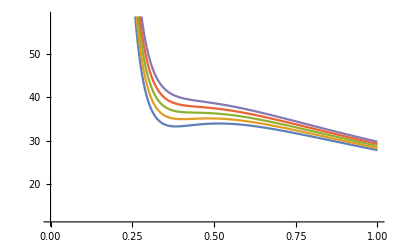

```mathematica
Plot[{P[x, 500],P[x,505],P[x,510],P[x,515],P[x,520]},{x,0,1}]
```

From the above plot, the best candidate for the true isotherm is T=510 K:

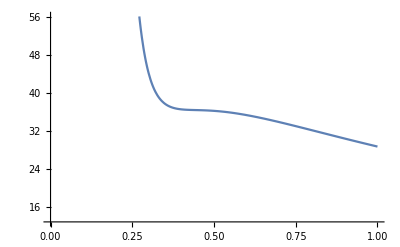

```mathematica
Plot[P[x,510],{x,0,1}]
```

And the critical pressure appears around 36 bar.1

Literature values: : Tc = 472.5 degrees F = ~517K, Pc=36.8 atm =~37.29 bar.

#### Ar:

One can begin by graphing isotherms over a large range of temperature and then gradually narrow the range, as I have below, landing on similar approximately-critical isotherms 2K apart.

```mathematica
P2[v_,t_] = (0.08314t)/(v-0.03201)-(1.355/v^2)
```

(0.08314 t)/(-0.03201+v)-1.355/v^2

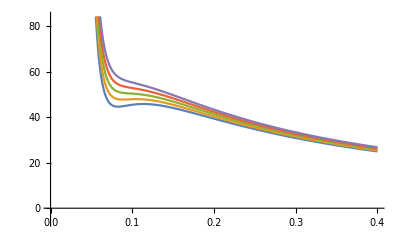

```mathematica
Plot[{P2[x, 148],P2[x,150],P2[x,152],P2[x,154],P2[x,156]},{x,0,0.4}]
```

Here, the critical isotherm appears around 152K and the critical pressure around 50 bar.
Indeed, the literature values: Tc=150.86K, Pc=48.9805 bar.2

## II. Hydrogen Orbital Wavefunctions

I wrote a package to automate conversion of spherical functions to Cartesian coordinates so they are compatible with ContourPlot3D.

```mathematica
<<SphericalMultivariatePlot`
```

For one-electron atoms, exact wavefunctions can be solved for and plotted. The wavefunctions for p and d orbitals are of the form:

```mathematica
Subscript[Ψ, nlm]=Subscript[Y, lm] Subscript[R, nl]
```

The angular portion Y is a function of θ and ϕ; the zeros thereof are the angular nodes. In general chemistry, a student may be asked to identify the orbital from the wavefunction and sketch a plot of that orbital’s shape and the corresponding node.

Here we will plot the real wavefunctions of the p orbitals, the planes corresponding to nodes, and the squares of the wavefunctions (in other words, the probability density).

First, a function to graph a plane3:

```mathematica
grid[{v1_,v2_},size_,color_]:={Lighting->"Neutral",FaceForm[Lighter@color],EdgeForm[color],Opacity[.9],Polygon[{(v1 #[[1]]+v2 #[[2]])+.5 (-v1-v2),(v1 #[[1]]+v2 #[[2]])+.5 (v1-v2),(v1 #[[1]]+v2 #[[2]])+.5 (v1+v2),(v1 #[[1]]+v2 #[[2]])+.5 (-v1+v2)}]&/@Tuples[Range[-size,size,1],{2}]}
```

Second, here is the association being used in the background to switch from spherical to Cartesian coordinates, for ease of plotting:

```mathematica
PolarToCartesian=Association[r->√(x^2+y^2+z^2),θ->cos^-1(z/r),ϕ->tan^-1(x,y)]
```

<|r→√(x^2+y^2+z^2),θ→ArcCos[z/r],ϕ→ArcTan[x,y]|>

Now for the orbitals.

The p_xorbital has an angular portion Sin[θ]Cos[ϕ]. The θ function has zeros on the positive and negative z-axis. The ϕ function has zeros at ϕ= π/2 and 3π/2. Those two lines together define the {y,z} plane; that plane is our node.

```mathematica
Ψ2px=fxSphericalToCartesian[(1^(3/2) r ⅇ^(-r/2) Sin[θ] Cos[ϕ])/(4 √(2 π))]
```

(ⅇ^(-1/2 √(x^2+y^2+z^2)) x)/(4 √(2 π))

```mathematica
Show[ContourPlot3D[Ψ2px,{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},Contours->{-0.05,0.05},AxesLabel->Automatic,PlotTheme->"WarmColor"],Graphics3D[grid[{{0,0,1},{0,1,0}},10,Blue],Opacity[0.5]]]
```

-Graphics3D-

Below is a contour plot of |Ψ|^2,  the probability distribution.

```mathematica
Show[ContourPlot3D[Abs[Ψ2px]^2,{x,-5.5,5.5},{y,-5.5,5.5},{z,-5.5,5.5},AxesLabel->Automatic],Graphics3D[grid[{{0,0,1},{0,1,0}},10,Blue],Opacity[0.5]]]
```

-Graphics3D-

The p_yorbital has an angular portion Sin[θ]Sin[ϕ]. The θ function has zeros on the positive and negative z-axis. The ϕ function has zeros at ϕ= 0 and π, a.k.a. the positive and negative x axis. Those two lines together define the {x,z} plane; that plane is our node.

```mathematica
Ψ2py=fxSphericalToCartesian[(1^(3/2) r ⅇ^(-r/2) Sin[θ] Sin[ϕ])/(4 √(2 π))]
```

(ⅇ^(-1/2 √(x^2+y^2+z^2)) y)/(4 √(2 π))

```mathematica
Show[ContourPlot3D[Ψ2py,{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},Contours->{-0.05,0.05},AxesLabel->Automatic,PlotTheme->"WarmColor"],Graphics3D[grid[{{0,0,1},{1,0,0}},10,Purple],Opacity[0.5]]]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[Abs[Ψ2py]^2,{x,-5.5,5.5},{y,-5.5,5.5},{z,-5.5,5.5},AxesLabel->Automatic],Graphics3D[grid[{{0,0,1},{1,0,0}},10,Purple],Opacity[0.5]]]
```

-Graphics3D-

```mathematica
Ψ2pz=fxSphericalToCartesian[(1^(3/2) r ⅇ^(-r/2) Cos[θ])/(4 √(2 π))]
```

(ⅇ^(-1/2 √(x^2+y^2+z^2)) z)/(4 √(2 π))

```mathematica
Show[ContourPlot3D[Ψ2pz,{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},Contours->{-0.05,0.05},AxesLabel->Automatic,PlotTheme->"WarmColor"],Graphics3D[grid[{{0,1,0},{1,0,0}},10,Green],Opacity[0.5]]]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[Abs[Ψ2pz]^2,{x,-5.5,5.5},{y,-5.5,5.5},{z,-5.5,5.5},AxesLabel->Automatic],Graphics3D[grid[{{0,1,0},{1,0,0}},10,Green],Opacity[0.5]]]
```

-Graphics3D-

## Further explorations

Biochemical kinetics equations could be handled easily using sliders in Manipulate[]; that may help students “play” with the variables and see what happens when one is varied.

For physical organic chemistry, manipulating MOJ plots in Mathematica might be an easy way to explore hypotheses about the effects of changing conditions on the mechanism of the reaction in question.

## Author contact information

msuther@mit.edu.

### End Notes

1	https://pubchem.ncbi.nlm.nih.gov/compound/Tetrachlorosilane

2	https://webbook.nist.gov/cgi/inchi?ID=C7440371&Mask=4

3	See https://mathematica.stackexchange.com/questions/102822/draw-grids-on-the-xy-xz-and-yz-planes